```mathematica
(* Applying our results in notebook "chemical langevin approximation", we can numerically search the whole enzymatic parameter range for {(Subscript[γ, x]^low,Δμ^low),(Subscript[γ, x]^high,Δμ^high)} scatter points (green and blue clouds) in Fig.3 of maintext.
```

```mathematica
(* If you want to run multiple jobs simultaneously with this algorithm on HPC for abundant scatter points generation, we suggest that you apply following code for each job to generate random parameters choices: 
Switch[$OperatingSystem,"MacOSX"|"Unix",NondeterministicRandomInteger[]:=AbortProtect@Module[{stream,res},stream=OpenRead["!head -c 4 /dev/random",BinaryFormat->True];
res=BinaryRead[stream,"UnsignedInteger32"];
Close[stream];
res],_,NondeterministicRandomInteger[]:=(Message[NondeterministicRandomInteger::notsupp,$OperatingSystem];$Failed)]
SeedRandom@NondeterministicRandomInteger[]; 
Note: Please ingnore above code if you do not need to run this algorithm on HPC*)

c=30.897*10^-15*6.02*10^23(*cell volume x Avogadro constant *);KB=c 5*10^-9 (*Set [K]=5 nM*);ku=kb KD;ρu=ρb KD2;KM=(kr+ku)/kb;KM2=(ρr+ρu)/ρb;
ρp=ρb P;

km=kr+ku;kp=kb S;k=km+kp;ρm=ρr+ρu;F=KB γk;SkB=(F S (F kb krr ρm+P γk (kb ρb ρr+krr ρrr ρu)))/(γk (F krr ku ρm+km P γk ρb ρr));SsB=(S (F kb kr ρm+km P γk ρrr ρu))/(F krr ku ρm+km P γk ρb ρr);
SpB=(P S (km P γk ρb ρrr+F (kb kr ρb+krr ku ρrr)))/(F krr ku ρm+km P γk ρb ρr);
(*Randomly pick parameters from the enzymatic parameter range. Symbol notation is same as notebook "chemical langevin approximation", KD/KD2 -> kinase/phosphatase Michaelis constants *)
rvtab[trials_]:=Table[{kr->10^RandomVariate[NormalDistribution[-0.06,1.18]],ρr->10^RandomVariate[NormalDistribution[-0.06,1.18]],kb->10^RandomVariate[NormalDistribution[3.94,1.12]]/c,ρb->10^RandomVariate[NormalDistribution[3.94,1.12]]/c,S->c 10^RandomVariate[NormalDistribution[-7.93,0.84]],P->c 10^RandomVariate[NormalDistribution[-7.93,0.84]],KD2->c 10^RandomVariate[NormalDistribution[-7.,1.31]],KD->c 10^RandomVariate[NormalDistribution[-7.,1.31]]},{trials}];
(*coefficients of power spectra *)
INc1=γk (KB^2 P SsB γk ρb (kb KB krr-kb ρr+krr ρr)^2+(kb KB S+ku SkB) γk (KB krr (SsB ρb+ρm)+P ρb ρr)^2+(KB krr S+kr SkB) γk (kb KB ((P+SsB) ρb+ρm)+P ρb ρr)^2+2 KB (KB (km-kr) krr (SsB ρb+ρm)+kb KB (krr SsB (KB+P+S+SsB) ρb+krr (KB+S+SsB) ρm+kr ((P+SsB) ρb+ρm))+kb P (KB+S) ρb ρr+P (km+krr SsB) ρb ρr)^2+KB^2 γk (krr (SsB ρb+ρm-ρr)-kb (KB krr+(P+SsB) ρb+ρm-ρr))^2 (SpB ρr+P S ρrr));INc2=γk (KB^2 krr^2 P SsB γk ρb+(KB krr S+kr SkB) γk (kb^2 KB^2+((P+SsB) ρb+ρm)^2-2 P ρb ρr)+(kb KB S+ku SkB) γk (KB^2 krr^2+2 KB krr P ρb+((P+SsB) ρb+ρm)^2-2 P ρb ρr)+2 KB ((KB krr (km-kr+SsB ρb+ρm)+(km+krr SsB) ((P+SsB) ρb+ρm)+kb (KB^2 krr+S ((P+SsB) ρb+ρm)+KB (kr+krr (S+SsB)+(P+SsB) ρb+ρm))+P ρb ρr)^2+2 (km+kb (KB+S)+krr (KB+SsB)+P ρb+SsB ρb+ρm) (-KB (km-kr) krr (SsB ρb+ρm)+kb KB (-(kr (P+SsB)+krr SsB (KB+P+S+SsB)) ρb-(kr+krr (KB+S+SsB)) ρm)-kb P (KB+S) ρb ρr-P (km+krr SsB) ρb ρr))+kb^2 KB^2 γk (SpB ρr+P S ρrr));INc4=γk ((KB krr S+kr SkB) γk+(kb KB S+ku SkB) γk+2 KB (-2 KB krr (km-kr+SsB ρb+ρm)+(km+kb (KB+S)+krr (KB+SsB)+P ρb+SsB ρb+ρm)^2-2 (km+krr SsB) ((P+SsB) ρb+ρm)-2 kb (KB^2 krr+S ((P+SsB) ρb+ρm)+KB (kr+krr (S+SsB)+(P+SsB) ρb+ρm))-2 P ρb ρr));INc6=2 KB γk;
Nc1=γk (2 KB (kb kr S-(kb KB+km-kr) krr SsB)^2 ((P+SsB) ρb+ρm)^2+(kb KB+km-kr)^2 (KB krr S+kr SkB) γk ((P+SsB) ρb+ρm)^2+kr^2 (kb KB S+ku SkB) γk ((P+SsB) ρb+ρm)^2+P SsB γk ρb (KB (kb KB+km-kr) krr-(kb KB+km) ρr)^2+γk (KB (km-kr) krr+km ((P+SsB) ρb+ρm-ρr)+kb KB (KB krr+(P+SsB) ρb+ρm-ρr))^2 (SpB ρr+P S ρrr));
Nc2=(2 KB γk (2 krr SsB (kb kr S-(kb KB+km-kr) krr SsB) ((P+SsB) ρb+ρm)+(kb (-kr S+KB krr SsB)+krr SsB (km-kr+(P+SsB) ρb+ρm))^2)+(kb KB S+ku SkB) (-2 kr (kr+krr SsB) γk ((P+SsB) ρb+ρm)+(krr SsB ((P+SsB) ρb+ρm)+kr (γk+(P+SsB) ρb+ρm))^2)+(KB krr S+kr SkB) (-2 (kb KB+km-kr) γk ((P+SsB) ρb+ρm) (km-kr+kb (KB+S)+γk+(P+SsB) ρb+ρm)+(-kr γk-kr P ρb-kr SsB ρb+P γk ρb+SsB γk ρb-kr ρm+γk ρm+km (γk+(P+SsB) ρb+ρm)+kb (S ((P+SsB) ρb+ρm)+KB (γk+(P+SsB) ρb+ρm)))^2)+P SsB ρb (2 γk (KB krr-ρr) (-KB (kb KB+km-kr) krr+(kb KB+km) ρr)+(KB krr (km-kr+kb (KB+S)+γk)-(km+kb (KB+S)+krr SsB+γk) ρr)^2)+(-2 γk (KB (km-kr) krr+km ((P+SsB) ρb+ρm-ρr)+kb KB (KB krr+(P+SsB) ρb+ρm-ρr)) (km+kb (KB+S)+krr (KB+SsB)+γk+P ρb+SsB ρb+ρm-ρr)+(km γk+KB krr (km-kr+γk)+km P ρb+km SsB ρb+krr P SsB ρb+krr SsB^2 ρb+P γk ρb+SsB γk ρb+km ρm+krr SsB ρm+γk ρm+kb (KB^2 krr+S ((P+SsB) ρb+ρm-ρr)+KB (krr S+γk+(P+SsB) ρb+ρm-ρr))-(km+krr SsB+γk) ρr)^2) (SpB ρr+P S ρrr));
Nc4=((kb KB S+ku SkB) (kr+krr SsB)^2+2 KB krr^2 SsB^2 γk+(KB krr S+kr SkB) ((km-kr+kb (KB+S))^2+2 kb S γk+γk^2+((P+SsB) ρb+ρm)^2)+P SsB ρb (-KB krr+ρr)^2+(km^2+KB krr (2 kr+KB krr)+kb^2 (KB+S)^2+2 km krr SsB+2 KB krr^2 SsB+krr^2 SsB^2+2 krr SsB γk+γk^2+2 kb ((KB+S) (km+krr SsB)+S γk)+2 KB krr P ρb+2 KB krr SsB ρb+P^2 ρb^2+2 P SsB ρb^2+SsB^2 ρb^2+2 KB krr ρm+2 P ρb ρm+2 SsB ρb ρm+ρm^2-2 (KB krr+(P+SsB) ρb+ρm) ρr+ρr^2) (SpB ρr+P S ρrr));
Nc6=(KB krr S+kr SkB+SpB ρr+P S ρrr);
Dc1=γk^2 (KB (km-kr) krr (SsB ρb+ρm)+km P ρb ρr+kb KB (KB krr (SsB ρb+ρm)+kr ((P+SsB) ρb+ρm)+P ρb ρr))^2;
Dc2=(-2 γk (km γk+km P ρb+km SsB ρb+krr P SsB ρb+krr SsB^2 ρb+P γk ρb+SsB γk ρb+km ρm+krr SsB ρm+γk ρm+KB krr (km-kr+γk+SsB ρb+ρm)+kb (KB^2 krr+S ((P+SsB) ρb+ρm)+KB (kr+krr (S+SsB)+γk+(P+SsB) ρb+ρm))+P ρb ρr) (KB (km-kr) krr (SsB ρb+ρm)+km P ρb ρr+kb KB (KB krr (SsB ρb+ρm)+kr ((P+SsB) ρb+ρm)+P ρb ρr))+(km P γk ρb+km SsB γk ρb+km γk ρm+KB krr (γk (SsB ρb+ρm)+km (γk+SsB ρb+ρm)-kr (γk+SsB ρb+ρm))+km P ρb ρr+krr P SsB ρb ρr+P γk ρb ρr+kb (KB^2 krr (γk+SsB ρb+ρm)+P S ρb ρr+KB (krr SsB (P+S+SsB) ρb+krr (S+SsB) ρm+γk ((P+SsB) ρb+ρm)+kr (γk+(P+SsB) ρb+ρm)+P ρb ρr)))^2);
Dc4=(2 kb KB kr P γk ρb+2 kb KB kr SsB γk ρb+2 kb KB^2 krr SsB γk ρb+2 KB km krr SsB γk ρb-2 KB kr krr SsB γk ρb+2 kb KB kr γk ρm+2 kb KB^2 krr γk ρm+2 KB km krr γk ρm-2 KB kr krr γk ρm+2 kb KB P γk ρb ρr+2 km P γk ρb ρr+(km γk+km P ρb+km SsB ρb+krr P SsB ρb+krr SsB^2 ρb+P γk ρb+SsB γk ρb+km ρm+krr SsB ρm+γk ρm+KB krr (km-kr+γk+SsB ρb+ρm)+kb (KB^2 krr+S ((P+SsB) ρb+ρm)+KB (kr+krr (S+SsB)+γk+(P+SsB) ρb+ρm))+P ρb ρr)^2-2 (km+kb (KB+S)+krr (KB+SsB)+γk+P ρb+SsB ρb+ρm) (km P γk ρb+km SsB γk ρb+km γk ρm+KB krr (γk (SsB ρb+ρm)+km (γk+SsB ρb+ρm)-kr (γk+SsB ρb+ρm))+km P ρb ρr+krr P SsB ρb ρr+P γk ρb ρr+kb (KB^2 krr (γk+SsB ρb+ρm)+P S ρb ρr+KB (krr SsB (P+S+SsB) ρb+krr (S+SsB) ρm+γk ((P+SsB) ρb+ρm)+kr (γk+(P+SsB) ρb+ρm)+P ρb ρr))));
Dc6=(km^2+KB krr (2 kr+KB krr)+kb^2 (KB+S)^2+2 km krr SsB+2 KB krr^2 SsB+krr^2 SsB^2+2 krr SsB γk+γk^2+2 kb (KB (km-kr)+S (km+krr SsB+γk))+2 KB krr P ρb+P^2 ρb^2+2 P SsB ρb^2+SsB^2 ρb^2+2 P ρb ρm+2 SsB ρb ρm+ρm^2-2 P ρb ρr);Dc8=1;Rho2[M_]:=1-2^(-2 M)(* ρ^2 as function of mutual information*);
(*power spectra constant Pn for noise*)
P1=2 γk KB;P2=kb KB S+ku SkB;P3=kr SkB+krr KB S;P4=ρb P SsB;P5=ρr SpB+ρrr S P;
(*coefficient of noise term ni for δX *)
a=Coefficient[((-(n2+n3) γk+n1 (km+krr SsB-ⅈ ω)) (P ρb ρr-ⅈ ((P+SsB) ρb+ρm) ω-ω^2)+KB krr (-(n2-n5) γk (SsB ρb+ρm)+(n4-n5) γk ρr+km n1 (SsB ρb+ρm-ⅈ ω)-kr n1 (SsB ρb+ρm-ⅈ ω)-ⅈ (-n2 γk+n4 γk+n1 SsB ρb+n1 ρm) ω-n1 ω^2)+kb (KB^2 krr (n4 γk-n5 γk+n1 (SsB ρb+ρm-ⅈ ω))+n1 S (P ρb ρr-ⅈ ((P+SsB) ρb+ρm) ω-ω^2)+KB (-n3 P γk ρb-n5 P γk ρb-n3 SsB γk ρb-n5 SsB γk ρb-n3 γk ρm-n5 γk ρm-n4 γk ρr+n5 γk ρr+n1 P ρb ρr+krr n1 (P SsB ρb+(S+SsB) (SsB ρb+ρm-ⅈ ω))+kr n1 ((P+SsB) ρb+ρm-ⅈ ω)-ⅈ (-(n3+n5) γk+n1 ((P+SsB) ρb+ρm)) ω-n1 ω^2)))/(KB krr (km-kr-ⅈ ω) (γk-ⅈ ω) (SsB ρb+ρm-ⅈ ω)-(km γk-ⅈ (km+krr SsB+γk) ω-ω^2) (-P ρb ρr+ⅈ ((P+SsB) ρb+ρm) ω+ω^2)+kb (KB^2 krr (γk-ⅈ ω) (SsB ρb+ρm-ⅈ ω)+S ω (-ⅈ P ρb ρr-((P+SsB) ρb+ρm) ω+ⅈ ω^2)+KB (kr (γk-ⅈ ω) ((P+SsB) ρb+ρm-ⅈ ω)-ⅈ (krr (S+SsB)+γk-ⅈ ω) (SsB ρb+ρm-ⅈ ω) ω+P ρb (γk ρr-ⅈ (krr SsB+γk+ρr) ω-ω^2)))),{n1,n2,n3,n4,n5}];
(*coefficient of noise term ni for δY*)
b=Coefficient[(-km krr n1 P SsB ρb+kr krr n1 P SsB ρb-km krr n1 SsB^2 ρb+kr krr n1 SsB^2 ρb-kr n2 P γk ρb+km n3 P γk ρb-kr n3 P γk ρb+km n5 P γk ρb-kr n2 SsB γk ρb+km n3 SsB γk ρb-kr n3 SsB γk ρb+km n5 SsB γk ρb-km krr n1 SsB ρm+kr krr n1 SsB ρm-kr n2 γk ρm+km n3 γk ρm-kr n3 γk ρm+km n5 γk ρm+km n4 γk ρr-km n5 γk ρr+ⅈ ((krr (n1+n2-n5) SsB-(n3+n5) γk) ((P+SsB) ρb+ρm)+kr (-krr n1 SsB+(n2+n3) (γk+(P+SsB) ρb+ρm))+(-n4+n5) (krr SsB+γk) ρr+km (krr n1 SsB-(n3+n5) (γk+(P+SsB) ρb+ρm)+(-n4+n5) ρr)) ω+(kr (n2+n3)-km (n3+n5)+krr n1 SsB+krr (n2-n5) SsB-(n3+n5) (γk+(P+SsB) ρb+ρm)-n4 ρr+n5 ρr) ω^2+ⅈ (n3+n5) ω^3+KB krr (n4-n5) (ⅈ (km-kr)+ω) (ⅈ γk+ω)-kb (KB^2 krr (n4-n5) (γk-ⅈ ω)+KB (krr n1 SsB ((P+SsB) ρb+ρm)-(n4 ρr+n3 ((P+SsB) ρb+ρm-ⅈ ω)+n5 ((P+SsB) ρb+ρm-ρr-ⅈ ω)) (γk-ⅈ ω)-ⅈ krr (n4 S-n5 S+n1 SsB) ω)+S (-kr n1 ((P+SsB) ρb+ρm)+ⅈ (kr n1+(n3+n5) ((P+SsB) ρb+ρm)+(n4-n5) ρr) ω+(n3+n5) ω^2)))/(KB krr (km-kr-ⅈ ω) (γk-ⅈ ω) (SsB ρb+ρm-ⅈ ω)-(km γk-ⅈ (km+krr SsB+γk) ω-ω^2) (-P ρb ρr+ⅈ ((P+SsB) ρb+ρm) ω+ω^2)+kb (KB γk (KB krr (SsB ρb+ρm)+kr ((P+SsB) ρb+ρm)+P ρb ρr)-ⅈ (KB ((krr SsB (P+S+SsB)+(P+SsB) γk) ρb+(krr (S+SsB)+γk) ρm+KB krr (γk+SsB ρb+ρm)+kr (γk+(P+SsB) ρb+ρm))+P (KB+S) ρb ρr) ω-(KB^2 krr+S ((P+SsB) ρb+ρm)+KB (kr+krr (S+SsB)+γk+(P+SsB) ρb+ρm)) ω^2+ⅈ (KB+S) ω^3)),{n1,n2,n3,n4,n5}];

(*Variance Y = 1/(2π)∫_(-∞)^∞ Subscript[P, YY](ω)dω*)
Vy[gk_Real,kar_,rhorr_,Pval_]:=Re[NIntegrate[(Nc1+Nc2 ω^2+Nc4 ω^4+Nc6 ω^6)/(2π (Dc1+Dc2 ω^2+Dc4 ω^4+Dc6 ω^6+ω^8))/.{γk->gk,ρrr->rhorr}/.krr->kar/.Pval,{ω,-∞,∞}]];

(*Variance X = 1/(2π)∫_(-∞)^∞ Subscript[P, XX](ω)dω*)
Vx[gk_Real,kar_,rhorr_,Pval_]:=Re[NIntegrate[(INc1+INc2 ω^2+INc4 ω^4+INc6 ω^6)/((2 π) (Dc1+Dc2 ω^2+Dc4 ω^4+Dc6 ω^6+ω^8))/.{γk->gk,ρrr->rhorr}/.krr->kar/.Pval,{ω,-∞,∞}]];
Pxyc=Conjugate[a] b; 
PXY=Pxyc.{P1,P2,P3,P4,P5};(*Subscript[P, XY](ω)*)
Covc[gk_Real,kar_,rhorr_,Pval_]:=If[Re[NIntegrate[PXY/(2 π)/.{γk->gk,ρrr->rhorr}/.krr->kar/.Pval,{ω,-∞,∞}]]<0,0,Re[NIntegrate[PXY/(2 π)/.{γk->gk,ρrr->rhorr}/.krr->kar/.Pval,{ω,-∞,∞}]]](* CoVariance XY = 1/(2π)∫_(-∞)^∞ Subscript[P, XY](ω)dω. Make sure that X and Y are not negative correlated*);
rho2[gk_Real,kar_,rhorr_,Pval_]:=Covc[gk,kar,rhorr,Pval]^2/(Vy[gk,kar,rhorr,Pval] Vx[gk,kar,rhorr,Pval])(* Pearson correlation coefficient square ρ^2 *);
Info[gk_Real,kar_,rhorr_,Pval_]:=-0.5 Log2[1-Covc[gk,kar,rhorr,Pval]^2/(Vy[gk,kar,rhorr,Pval] Vx[gk,kar,rhorr,Pval])](*Mutual information -0.5 Log2[1-ρ^2]*);

fg[gk_Real,dg_Real,Pvals_]:=FindMaximum[rho2[gk,10^x*kr,(E^-dg kr ρr)/krr (kb/ku) (ρb/ρu),Pvals],{x,Floor[-Log10[ⅇ^dg KD KD2]/.Pvals]+Floor[Log10[ⅇ^dg KD KD2]/.Pvals]/10(Ordering[Table[rho2[gk,10^x*kr,(E^-dg kr ρr)/krr (kb/ku) (ρb/ρu),Pvals],{x,Floor[-Log10[ⅇ^dg KD KD2]/.Pvals],0,Floor[Log10[ⅇ^dg KD KD2]/.Pvals]/10}],-1][[1]]-1)},Method->"PrincipalAxis"][[1]]//Quiet (*Function of Maximum ρ^2 (also Maximum  mutual information) ->  F(Subscript[γ, K], Δμ, parameters choice): x from Subscript[κ, -r]= 10^x*Subscript[κ, r] as free parameter. Picking 10 points through the range of x, then set the point given maximized ρ^2 as starting point for numerical search    *);
fg2[gk_Real,dg_Real,Pvals_]:=FindMaximum[rho2[gk,10^x*kr,(E^-dg kr ρr)/krr (kb/ku) (ρb/ρu),Pvals],{x,Floor[-Log10[ⅇ^dg KD KD2]/.Pvals]+Floor[Log10[ⅇ^dg KD KD2]/.Pvals]/10(Ordering[Table[rho2[gk,10^x*kr,(E^-dg kr ρr)/krr (kb/ku) (ρb/ρu),Pvals],{x,Floor[-Log10[ⅇ^dg KD KD2]/.Pvals],0,Floor[Log10[ⅇ^dg KD KD2]/.Pvals]/10}],-1][[1]]-1)},Method->"PrincipalAxis"][[2]]//Quiet (*Function of coefficient x -> F2(Subscript[γ, K], Δμ, parameters choice) when maximum ρ^2 (also mutual information) achieved *);
C1= (F krr ku ρm+km P γk ρb ρr);C2=S(F kb krr ρm+P γk (kb ρb ρr+krr ρrr ρu));
BW[M_,Pvals_]:=Quiet[Select[γk/.NSolve[Simplify[(γk C1)/(C1+C2)==((kr C2)/(C1+C2))/(4^(M+1)(4^M-1))/.Pvals/.{krr->0,ρrr->0}],γk],#1>0&]⟦1⟧](*Upper bound of bandwidth given by Eq.(5) in main text*);

BWT[M_,BW_,Pvals_]:=Quiet[γk/.FindRoot[Rho2[M]==rho2[γk,0,0,Pvals],{γk,BW}]](* The bandwidth of Subscript[γ, K] while both reverse rate Subscript[κ, -r] = Subscript[ρ, -r] = 0  *);
RBW[M_,BWT_,Pvals_]:=Quiet[γk/.FindRoot[Rho2[M]==fg[γk,100.0,Pvals],{γk,BWT}]](*The numerical bandwidth of Subscript[γ, K]: set Δμ=100 as cutoff for infinite chemical potential*);
(*Generating scatter points*)
m=1;(*target mutual information*)
runt=AbsoluteTiming[{n=100;BigData=rvtab[n](*randomly pick parameters from enzymatic parameter range for n times*);
bdw=Quiet[Table[BW[m,BigData[[i]]],{i,1,n}]](*calculate BW bandwidth for all parameters choice*);
filtered=Position[bdw,_?(#1>1/10^5&),1]//Flatten(*Filter for BW bandwidth > 1/10^5 that give biological reasonable Subscript[γ, x]^low and Subscript[γ, x]^high*);
FData=BigData[[filtered]](*Corresponding parameters choice*);
nbdw=Quiet[Table[BWT[m,bdw⟦i⟧,BigData⟦i⟧],{i,filtered}]](*calculate BWT bandwidth for all filtered parameters choice*);
c1=Table[rho2[nbdw[[i]],0,0,FData[[i]]],{i,1,Length[FData]}]//Quiet(*calculate ρ^2 for all filtered parameters choice*);
filtered2=Flatten[Intersection[Position[nbdw,_?(#1>1/10^5&),1],Position[Abs[c1-Rho2[m]],_?(#1<0.001&),1]]](*Filter for BWT bandwidth > 1/10^5 & Mutual information = m *);
(*generate filtered2 bandwidth Sbdw and corresponding parameters choice SData *)
Sbdw=nbdw[[filtered2]];
SData=FData[[filtered2]];
prbdw=Table[RBW[m,Sbdw[[i]],SData[[i]]],{i,1,Length[SData]}](*calculate RBW bandwidth for all filtered2 parameters choice*);
filtered3=Position[prbdw,_?(#1>1/10^5&),1]//Flatten(*Filter for RBW bandwidth > 1/10^5 *);
(*generate filtered3 bandwidth rbdw and corresponding parameters choice PBData *)
rbdw=prbdw[[filtered3]];
PBData=SData[[filtered3]];
Covc[gk_Real,kar_,rhorr_,Pval_]:=Re[NIntegrate[PXY/(2 π)/.{γk->gk,ρrr->rhorr}/.krr->kar/.Pval,{ω,-∞,∞}]](* apply CoVariance XY = 1/(2π)∫_(-∞)^∞ Subscript[P, XY](ω)dω again for numerical search consistence*);
dm3[M_,bw_,Pvals_]:=Quiet[{{bw/10^2,δu/.FindRoot[Rho2[M]==fg[bw/10^2,δu,Pvals],{δu,0,8}]},{0.95 bw,δu/.FindRoot[Rho2[M]==fg[0.95 bw,δu,Pvals],{δu,0,10}]}}](*Function for green and blue points in maintext {(Subscript[γ, x]^low,Δμ^low),(Subscript[γ, x]^high,Δμ^high)}*);
deltaMuLEpEF[deltaMupoints_,Pvals_]:={{ρrr,krr}/.ρrr->((E^-deltaMupoints[[1,2]] kr ρr) kb ρb)/(krr ku ρu)/.krr->10^x kr/.fg2[deltaMupoints[[1,1]],deltaMupoints[[1,2]],Pvals]/.Pvals,{ρrr,krr}/.ρrr->((E^-deltaMupoints[[2,2]] kr ρr) kb ρb)/(krr ku ρu)/.krr->10^x kr/.fg2[deltaMupoints[[2,1]],deltaMupoints[[2,2]],Pvals]/.Pvals}(* Function for reverse rates {{Subscript[ρ, -r],Subscript[κ, -r]},{Subscript[ρ, -r],Subscript[κ, -r]}} of above two points *);
Quiet[points=Table[dm3[m,rbdw[[i]],PBData[[i]]],{i,1,Length[rbdw]}]](*green and blue points from maintext {(Subscript[γ, x]^low,Δμ^low),(Subscript[γ, x]^high,Δμ^high)}*);
Quiet[rerates=Table[deltaMuLEpEF[points[[i]],PBData[[i]]],{i,1,Length[PBData]}]](* reverse rates {{Subscript[ρ, -r],Subscript[κ, -r]},{Subscript[ρ, -r],Subscript[κ, -r]}} of above two points *);}];Print[{runt[[1]],rbdw,PBData,points,rerates}]
```

```mathematica
(*Set \data as input directory*)
SetDirectory[NotebookDirectory[]];
SetDirectory[FileNameJoin[{NotebookDirectory[],Select[FileNames["*","",Infinity],DirectoryQ][[1]]}]]
```

```mathematica
(*Applying our data for 1 bit generated by above algorithm, we will reproduce the Fig.3 D and G in maintext*)
```

```mathematica
rbdw=Get["rbdw(5nmKB,precise,1).out"];(* Filtered parameters' Bandwidth *)
PBData=Get["PBData(5nmKB,precise,1).out"];(* Corresponding Parameters *)
points=Get["points(5nmKB,precise,1).out"];(* Two points {(Subscript[γ, x]^low,Δμ^low),(Subscript[γ, x]^high,Δμ^high)} *)
rerates=Get["rerates(5nmKB,precise,1).out"](* reverse rates {{Subscript[ρ, -r],Subscript[κ, -r]},{Subscript[ρ, -r],Subscript[κ, -r]}} for two points *);
```

```mathematica
c=30.897*10^-15*6.02*10^23(*volume * Avogadro constant *);KB=c 5*10^-9 (*Set [K]=5 nM*);ku=kb KD;ρu=ρb KD2;KM=(kr+ku)/kb;KM2=(ρr+ρu)/ρb;
ρp=ρb P;

km=kr+ku;kp=kb S;k=km+kp;ρm=ρr+ρu;F=KB γk;SkB=(F S (F kb krr ρm+P γk (kb ρb ρr+krr ρrr ρu)))/(γk (F krr ku ρm+km P γk ρb ρr));SsB=(S (F kb kr ρm+km P γk ρrr ρu))/(F krr ku ρm+km P γk ρb ρr);
SpB=(P S (km P γk ρb ρrr+F (kb kr ρb+krr ku ρrr)))/(F krr ku ρm+km P γk ρb ρr);
```

```mathematica
C1= (F krr ku ρm+km P γk ρb ρr);C2=S(F kb krr ρm+P γk (kb ρb ρr+krr ρrr ρu));(* check our SI for more details*)
```

```mathematica
le=Length[rbdw];γxTab=Table[(γk C1)/(C1+C2)/.{γk->points⟦ii,i,1⟧,ρrr->rerates⟦ii,i,1⟧,krr->rerates⟦ii,i,2⟧}/.PBData⟦ii⟧,{ii,1,le},{i,1,2}];R0Tab=Table[(kr C2)/(C1+C2)/.{γk->points⟦ii,i,1⟧,ρrr->rerates⟦ii,i,1⟧,krr->rerates⟦ii,i,2⟧}/.PBData⟦ii⟧,{ii,1,le},{i,1,2}];
```

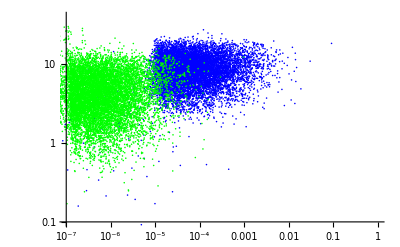

```mathematica
(*1 bit Fig.3 D*)
ListLogLogPlot[{Inner[List,γxTab[[All,2]],points[[All,2,2]],List],Inner[List,γxTab[[All,1]],points[[All,1,2]],List]},PlotRange->{{10^-7,1},{10^-1,40}},PlotStyle->{Blue,Green}]
```

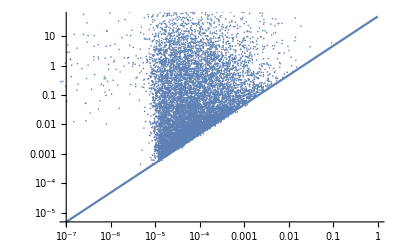

```mathematica
g1=LogLogPlot[4^(II+1)(4^II-1)x/.{II->1},{x,1*^-7,1}](*upper bound for Subscript[γ, x] Eq.(5) in maintext for I = 1bit*);
g2=ListLogLogPlot[Inner[List,γxTab[[All,2]],R0Tab[[All,2]],List],PlotRange->{{10^-8,.100000},All}];
Show[g1,g2](* Fig.3 G*)
```

```mathematica
(*similarly, applying our data for 1.5/2 bits generated by above algorithm, we reproduce the Fig.3 E/F/H/I in maintext*)
```

```mathematica
(*1.5 bits *)
rbdw=Get["rbdw(5nmKB,precise,1.5).out"];
PBData=Get["PBData(5nmKB,precise,1.5).out"];
points=Get["points(5nmKB,precise,1.5).out"];
rerates=Get["rerates(5nmKB,precise,1.5).out"];
```

```mathematica
c=30.897*10^-15*6.02*10^23(*volume * Avogadro constant *);KB=c 5*10^-9 (*Set [K]=5 nM*);ku=kb KD;ρu=ρb KD2;KM=(kr+ku)/kb;KM2=(ρr+ρu)/ρb;
ρp=ρb P;

km=kr+ku;kp=kb S;k=km+kp;ρm=ρr+ρu;F=KB γk;SkB=(F S (F kb krr ρm+P γk (kb ρb ρr+krr ρrr ρu)))/(γk (F krr ku ρm+km P γk ρb ρr));SsB=(S (F kb kr ρm+km P γk ρrr ρu))/(F krr ku ρm+km P γk ρb ρr);
SpB=(P S (km P γk ρb ρrr+F (kb kr ρb+krr ku ρrr)))/(F krr ku ρm+km P γk ρb ρr);
```

```mathematica
C1= (F krr ku ρm+km P γk ρb ρr);C2=S(F kb krr ρm+P γk (kb ρb ρr+krr ρrr ρu));(* check our SI for more details*)
```

```mathematica
le=Length[rbdw];γxTab=Table[(γk C1)/(C1+C2)/.{γk->points⟦ii,i,1⟧,ρrr->rerates⟦ii,i,1⟧,krr->rerates⟦ii,i,2⟧}/.PBData⟦ii⟧,{ii,1,le},{i,1,2}];R0Tab=Table[(kr C2)/(C1+C2)/.{γk->points⟦ii,i,1⟧,ρrr->rerates⟦ii,i,1⟧,krr->rerates⟦ii,i,2⟧}/.PBData⟦ii⟧,{ii,1,le},{i,1,2}];
```

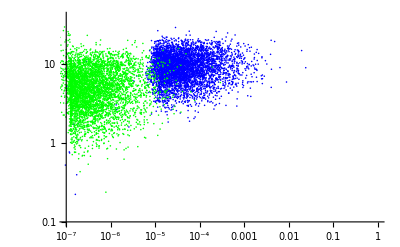

```mathematica
(*1.5 bits Fig.3 E*)
ListLogLogPlot[{Inner[List,γxTab[[All,2]],points[[All,2,2]],List],Inner[List,γxTab[[All,1]],points[[All,1,2]],List]},PlotRange->{{10^-7,1},{10^-1,40}},PlotStyle->{Blue,Green}]
```

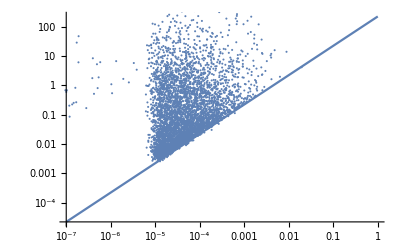

```mathematica
g3=LogLogPlot[4^(II+1)(4^II-1)x/.{II->1.5},{x,1*^-7,1}](*upper bound for Subscript[γ, x] Eq.(5) in maintext for I = 1.5 bits*);
g4=ListLogLogPlot[Inner[List,γxTab[[All,2]],R0Tab[[All,2]],List],PlotRange->{{10^-8,.100000},All}];
Show[g3,g4](* Fig.3 H*)
```

```mathematica
(*2 bits *)
rbdw=Get["rbdw(5nmKB,precise,2).out"];
PBData=Get["PBData(5nmKB,precise,2).out"];
points=Get["points(5nmKB,precise,2).out"];
rerates=Get["rerates(5nmKB,precise,2).out"];
```

```mathematica
c=30.897*10^-15*6.02*10^23(*volume * Avogadro constant *);KB=c 5*10^-9 (*Set [K]=5 nM*);ku=kb KD;ρu=ρb KD2;KM=(kr+ku)/kb;KM2=(ρr+ρu)/ρb;
ρp=ρb P;

km=kr+ku;kp=kb S;k=km+kp;ρm=ρr+ρu;F=KB γk;SkB=(F S (F kb krr ρm+P γk (kb ρb ρr+krr ρrr ρu)))/(γk (F krr ku ρm+km P γk ρb ρr));SsB=(S (F kb kr ρm+km P γk ρrr ρu))/(F krr ku ρm+km P γk ρb ρr);
SpB=(P S (km P γk ρb ρrr+F (kb kr ρb+krr ku ρrr)))/(F krr ku ρm+km P γk ρb ρr);
```

```mathematica
C1= (F krr ku ρm+km P γk ρb ρr);C2=S(F kb krr ρm+P γk (kb ρb ρr+krr ρrr ρu));(* check our SI for more details*)
```

```mathematica
le=Length[rbdw];γxTab=Table[(γk C1)/(C1+C2)/.{γk->points⟦ii,i,1⟧,ρrr->rerates⟦ii,i,1⟧,krr->rerates⟦ii,i,2⟧}/.PBData⟦ii⟧,{ii,1,le},{i,1,2}];R0Tab=Table[(kr C2)/(C1+C2)/.{γk->points⟦ii,i,1⟧,ρrr->rerates⟦ii,i,1⟧,krr->rerates⟦ii,i,2⟧}/.PBData⟦ii⟧,{ii,1,le},{i,1,2}];
```

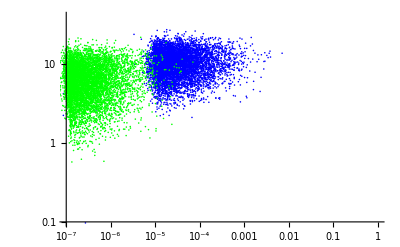

```mathematica
(*2 bits Fig.3 F*)
ListLogLogPlot[{Inner[List,γxTab[[All,2]],points[[All,2,2]],List],Inner[List,γxTab[[All,1]],points[[All,1,2]],List]},PlotRange->{{10^-7,1},{10^-1,40}},PlotStyle->{Blue,Green}]
```

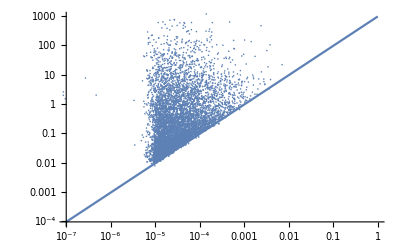

```mathematica
g5=LogLogPlot[4^(II+1)(4^II-1)x/.{II->2},{x,1*^-7,1}](*upper bound for Subscript[γ, x] Eq.(5) in maintext for I = 2 bits*);
g6=ListLogLogPlot[Inner[List,γxTab[[All,2]],R0Tab[[All,2]],List],PlotRange->{{10^-8,.100000},All}];
Show[g5,g6](* Fig.3 I*)
```